```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
SqExp[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]^2/(2 ℓ^2)]
OrnsteinUhlenbeck[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]/ℓ]
Matern[ν_][ℓ_][a_,b_]:=With[{r=EuclideanDistance[a,b]},
2^(1-ν)/Gamma[ν]((√(2ν)r)/ℓ)^ν BesselK[ν,(√(2ν)r)/ℓ]]

SqExpC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]^2/(2 ℓ^2)]]
OrnsteinUhlenbeckC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]/ℓ]]

Block[{ℓ,a,b},
Matern[3/2][ℓ_][a_,b_]:=Evaluate[Matern[3/2][ℓ][a,b]//FullSimplify];
Matern[5/2][ℓ_][a_,b_]:=Evaluate[Matern[5/2][ℓ][a,b]//FullSimplify];
Matern[7/2][ℓ_][a_,b_]:=Evaluate[Matern[7/2][ℓ][a,b]//FullSimplify]]
```

```mathematica
Krig[Kernel_,X_,Y_]:=
With[{Σ22=Outer[Kernel,X,X]},
With[{Σ22i=LinearSolve[Σ22,Method->"Cholesky"]},
Compile[{{p,_Real}},
Module[{μ,Σ,Σ11,Σ12,Σ21,σ},
Σ11=Outer[Kernel,{p},{p}];
Σ12=Outer[Kernel,{p},X];
Σ21=Transpose[Σ12];
μ=Dot[Σ12,Σ22i[Y]]//First;
Σ=Σ11-Dot[Σ12,Σ22i[Σ21]];
σ=Σ⟦1,1⟧;
{μ,σ}],
RuntimeOptions->{
"EvaluateSymbolically"->False},
CompilationOptions->{
"ExpressionOptimization"->True,
"InlineExternalDefinitions"->True,
"InlineCompiledFunctions"->True}]]]
```

```mathematica
With[{
Y={0,1/4,-1/4,1,0},
X={1/10,1/4,1/2,3/4,9/10}},
Krig[SqExpC[0.1],X,Y]];
```

```mathematica
KrigPlot[Kernel_,X_,Y_,t_]:=
With[{f=Krig[K,X,Y]},
Block[{μ,σ,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ},{μ,σ}=f[x];body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ^2],
high=plotf[μ+σ^2]
},
Plot[{mean[x],low[x],high[x]},{x,0,1},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None},
Filling->{2->{3}}]
]]]
```

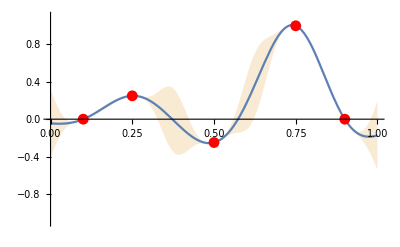

```mathematica
With[{
Y={0,1/4,-1/4,1,0},
X={1/10,1/4,1/2,3/4,9/10}},
Show[
KrigPlot[SqExpC[0.1],X,Y],
ListPlot[Transpose[{X,Y}],
PlotStyle->Red]]]
```

```mathematica
Manipulate[
Module[{X,Y},
{X,Y}=Transpose[p];
KrigPlot[Kernel[l],X,Y]],
{{p,{{1/2,3/4},{3/4,-3/4},{1/4,-1/10}}},
{0,-1},{1,1},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{l,0.1},0.01,0.2},SaveDefinitions->True]
```

```mathematica
ExpectedGainC=
Compile[{{μ,_Real},{σ,_Real},{ts,_Real}},
Module[{t},
t=(ts-μ)/σ;
σ((ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)])],
CompilationOptions->{"ExpressionOptimization" -> False}]

With[{b=2^(√(2 π))},
ExpectedGainC=
Compile[{{μ,_Real},{σ,_Real},{ts,_Real}},
Module[{t},
t=(ts-μ)/σ;
σ(Log[b,1+b^-t])],
CompilationOptions->{"ExpressionOptimization" -> False}]]
```

CompiledFunction[…]

CompiledFunction[…]

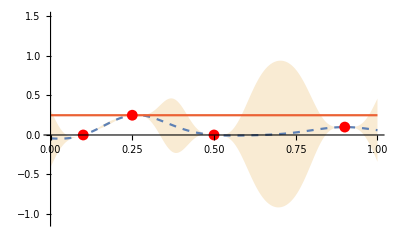

```mathematica
ExpectedGainPlot[Kernel_,X_,Y_,t_]:=
With[{f=Krig[Kernel,X,Y]},
Block[{μ,σ,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ},{μ,σ}=f[x];body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ^2],
high=plotf[μ+σ^2],
exgain=plotf[ExpectedGain[μ,σ,t]]
},
Plot[{mean[x],low[x],high[x],t,exgain[x]},{x,0,1},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]

With[{
Y={0,1/4,0,1/10},
X={1/10,1/4,1/2,9/10}},
Show[
ExpectedGainPlot[SqExp[0.1],X,Y,1/4],
ListPlot[Transpose[{X,Y}],
PlotStyle->Red]]]
```

```mathematica
Manipulate[
Module[{X,Y,f,t},
{X,Y}=Transpose[p];
t=Max[Y];
ExpectedGainPlot[Kernel[l],X,Y,t]],
{{p,{{1/2,0},{1/4,1/4},{9/10,1/10}}},
{0,-1},{1,1.5},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{l,0.1},0.01,0.2},SaveDefinitions->True]
```

```mathematica
With[{
t=0.1,
Y={0,1/4,-1/4,0},
X={1/10,1/4,1/2,9/10}},
Module[{f,exgain},
f=Krig[SqExp[0.1],X,Y];
exgain=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];ExpectedGainC[μ,σ,t]],
"RuntimeOptions"->{
"EvaluateSymbolically"->False}];
NMaximize[{exgain[x],x>0&&x<1},x]]]
```

{0.322653,{x→0.712578}}

1

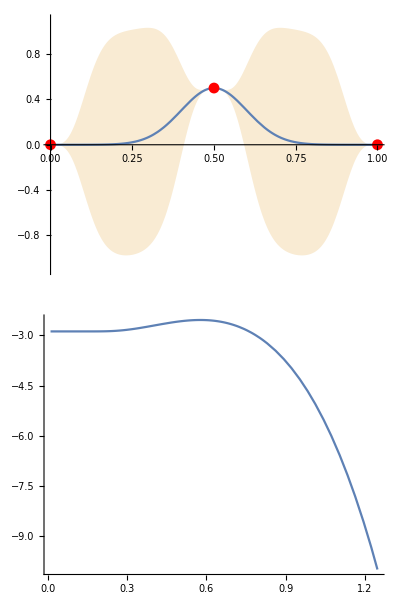

```mathematica
L=1
With[{
Y={0,1/2,0},
X={0,L/2,L}},
With[{f=Compile[{{l,_Real}},
Block[{Σ22=Outer[SqExp[l],X,X]},
LogLikelihood[
MultinormalDistribution[ConstantArray[0,Length[X]],Σ22],
{Y}]]]},
Column[{
Show[
KrigPlot[SqExpC[0.1],X,Y],
ListPlot[Transpose[{X,Y}],PlotStyle->Red]],
Plot[f[x],{x,0.01,3L/2},PlotRange->{0,-10}]}]]]
```

```mathematica
KrigMAP[Kernel_,X_,Y_]:=
Block[{f,l},
f=Compile[{{l,_Real}},
Module[{Σ22=Outer[Kernel[l],X,X]},
LogLikelihood[
MultinormalDistribution[ConstantArray[0,Length[X]],Σ22],
{Y}]],
"RuntimeOptions"->{
"EvaluateSymbolically"->False}];
NMaximize[{f[l],l>0&&l<1},l,
PrecisionGoal->2,
AccuracyGoal->2]]
```

```mathematica
L=0.2;
With[{
Y={0,1/2,0},
X={0,L/2,L}},
KrigMAP[SqExpC,X,Y]]
```

{-2.5404,{l→0.115429}}

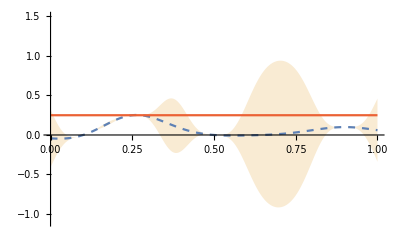

```mathematica
ExpectedGainPlotFoo[Kernel_,X_,Y_,t_]:=
With[
{f=Krig[Kernel,X,Y]},
Block[{μ,σ,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ},{μ,σ}=f[x];body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ^2],
high=plotf[μ+σ^2],
exgain=plotf[ExpectedGain[μ,σ,t]]
},
Plot[{mean[x],low[x],high[x],t,exgain[x]},{x,0,1},
Method->{Compiled->False},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]

With[{
Y={0,1/4,0,1/10},
X={1/10,1/4,1/2,9/10}},
ExpectedGainPlotFoo[SqExpC[0.1],X,Y,1/4]]
```

```mathematica
Expectation[Max[0,(x-t)],x\[Distributed]NormalDistribution[μ,σ]]
%//Expand//FullSimplify
Expectation[Max[0,(x-t)],x\[Distributed]NormalDistribution[]]
σ %/.t->(t-μ)/σ//Expand//FullSimplify
```

-(ⅇ^(-(t-μ)^2/(2 σ^2)) (-√2 σ+ⅇ^((t-μ)^2/(2 σ^2)) √π t Erfc[(t-μ)/(√2 σ)]-ⅇ^((t-μ)^2/(2 σ^2)) √π μ Erfc[(t-μ)/(√2 σ)]))/(2 √π)

(ⅇ^(-(t-μ)^2/(2 σ^2)) σ)/(√(2 π))+1/2 (-t+μ) Erfc[(t-μ)/(√2 σ)]

-(ⅇ^(-t^2/2) (-√2+ⅇ^(t^2/2) √π t Erfc[t/(√2)]))/(2 √π)

(ⅇ^(-(t-μ)^2/(2 σ^2)) σ)/(√(2 π))+1/2 (-t+μ) Erfc[(t-μ)/(√2 σ)]

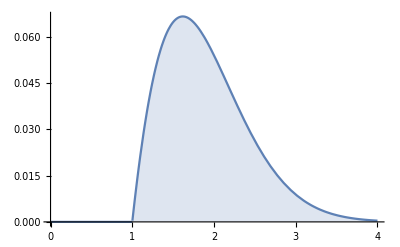

```mathematica
With[{t=1},
Plot[{PDF[NormalDistribution[],x] Max[0,(x-t)]},{x,0,4},Filling->Bottom]]
```

```mathematica
Expand[(ts-μ)/σ]
```

ts/σ-μ/σ

```mathematica
Expectation[x\[Conditioned]x>t,x\[Distributed]NormalDistribution[]]
```

(ⅇ^(-t^2/2) √(2/π))/Erfc[t/(√2)]

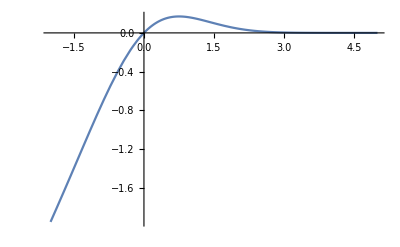

```mathematica
Plot[1/2 t Erfc[t/(√2)],{t,-2,5}]
```

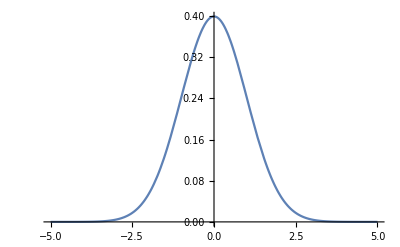

```mathematica
Plot[(ⅇ^(-t^2/2))/(√(2 π)),{t,-5,5}]
```

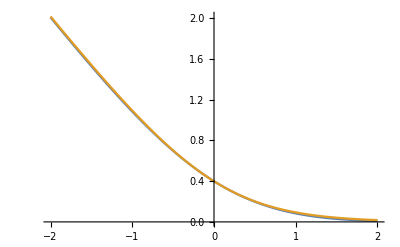

```mathematica
With[{b=2^(√(2 π))},
Plot[{(ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)],Log[b,1+b^-t]},{t,-2,2}]]
```

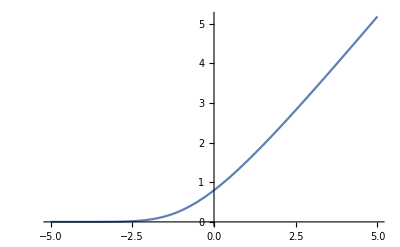

```mathematica
Plot[(ⅇ^(-t^2/2) √(2/π))/Erfc[t/(√2)],{t,-5,5}]
```

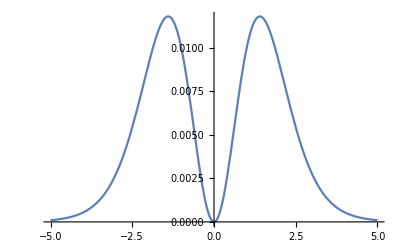

```mathematica
With[{b=2^(√(2 π))},
Plot[Abs[(ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)]-Log[b,1+b^-t]],{t,-5,5}]]
```

```mathematica
opt[b_?NumericQ]:= NIntegrate[((ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)]-Log[b,1+b^-t])^2,{t,-∞,∞}]
```

```mathematica
NMinimize[{opt[b],b>5&&b<6},b]
```

{0.000231466,{b→5.90854}}

```mathematica
Integrate[x(ⅇ^(-x^2/2))/(√(2 π)),{x,t,∞}]
Integrate[x(ⅇ^(-x^2/2))/(√(2 π)),x]
```

(ⅇ^(-t^2/2))/(√(2 π))

-(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Dt[(ⅇ^(-x^2/2))/(√(2 π)),x]
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

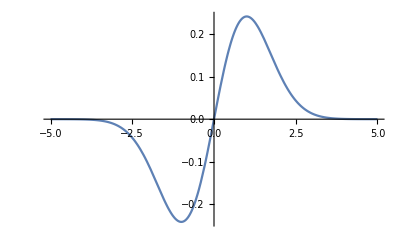

```mathematica
Plot[x(ⅇ^(-x^2/2))/(√(2 π)),{x,-5,5}]
```

```mathematica
Series[(ⅇ^(-t^2/2))/(√(2 π)),{t,0,4}]
```

1/(√(2 π))-t^2/(2 √(2 π))+t^4/(8 √(2 π))+O[t]^5

```mathematica
Series[1/2 t Erfc[t/(√2)],{t,0,4}]
```

t/2-t^2/(√(2 π))+t^4/(6 √(2 π))+O[t]^5

```mathematica
Series[Log[b,1+b^-t],{t,0,4}]
```

Log[2]/Log[b]-t/2+1/8 Log[b] t^2-1/192 Log[b]^3 t^4+O[t]^5

```mathematica
N[59/10]
```

5.9

```mathematica
Series[(ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)],{t,0,4}]//Normal
```

1/(√(2 π))-t/2+t^2/(2 √(2 π))-t^4/(24 √(2 π))

```mathematica
Solve[{Log[2]/Log[b]==1/(√(2 π))},b]
```

{{b→2^(√(2 π))}}

```mathematica
Matern[3/2][ℓ][a,b]//FullSimplify
```

(ⅇ^(-(√3 EuclideanDistance[a,b])/ℓ) (ℓ+√3 EuclideanDistance[a,b]))/ℓ

```mathematica
Matern[5/2][ℓ][a,b]
```

(ⅇ^(-(√5 EuclideanDistance[a,b])/ℓ) (3 ℓ^2+3 √5 ℓ EuclideanDistance[a,b]+5 EuclideanDistance[a,b]^2))/(3 ℓ^2)